```mathematica
Quit[];
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.11 (2 Sep 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (6 Oct 2019)

by Thomas Hahn

```mathematica
(* Create my topologies. *)
(* 0 loops, 2 incoming legs, 2 outgoing legs.*)
topologies=CreateTopologies[0,2 -> 2];
_Hel=0;
Print[topologies];
```

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

loading generic model file /Users/kpachal/Code/DMSP/FormCalc/FeynArts-3.11/Models/DMsimp_s_spin1_vector.gen

> $GenericMixing is OFF

generic model {DMsimp_s_spin1_vector} initialized

loading classes model file /Users/kpachal/Code/DMSP/FormCalc/FeynArts-3.11/Models/DMsimp_s_spin1_vector.mod

> 46 particles (incl. antiparticles) in 26 classes

> $CounterTerms are ON

> 147 vertices

> 48 counterterms of order 1

classes model {DMsimp_s_spin1_vector} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 1 Classes insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

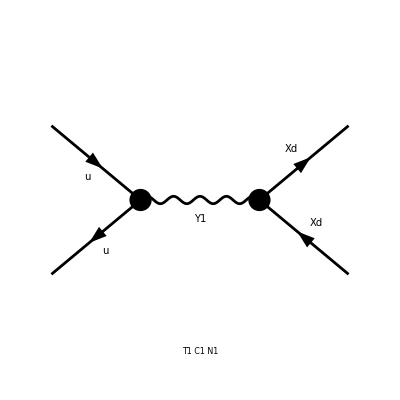

```mathematica
(* ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]} *)
diagvec=InsertFields[topologies,{F[7,{1}],-F[7,{1}]}->{F[13],-F[13]},InsertionLevel->{Classes},
Model->"DMsimp_s_spin1_vector",
GenericModel->"DMsimp_s_spin1_vector"];
Paint[diagvec];
```

```mathematica
(* Calculate amplitude. *)
ClearProcess[];
amplist = CreateFeynAmp[diagvec];
amp=CalcFeynAmp[amplist,FermionChains->VA];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/kpachal/fc-amp-9.frm

running FORM...

ok

```mathematica
(* Done with FeynArts! Time to pass the amplitude to FormCalc. *)
(* Squared matrix elements; evaluate *)
squared = SquaredME[amp];
Print[squared];
```

{FF[F1] FFC[F1] Mat[F1,F1],{FF[F1]→-gc75 gc76 Den[S,MY1^2],FFC[F1]→-(gc75Superscript[*]) (gc76Superscript[*]) Den[S,(MY1Superscript[*])^2]}}

```mathematica
(* SquaredME returns a list of {squared, squaredRules}, where we should later apply "squaredRules" to "squared". *)
(* Because of the quarks, we do ColorME too. *)
cleanSquaredME = squared[[1]]//.squared[[2]]//.HelicityME[amp]//FullSimplify
```

> 1 helicity matrix elements

preparing FORM code in /Users/kpachal/fc-hel-10.frm

running FORM...

ok

1/2 gc75 gc76 (T^2+2 MXd^2 (MXd^2+S-T-U)+U^2) (gc75Superscript[*]) (gc76Superscript[*]) Den[S,MY1^2] Den[S,(MY1Superscript[*])^2]

```mathematica
(* We want to sum over polarisations and make them go away: *)
TotalME = PolarizationSum[cleanSquaredME,GaugeTerms->False]//.Subexpr[]//.Abbr[]
```

preparing FORM code in /Users/kpachal/fc-pol-10.frm

running FORM...

ok

1/2 gc75 gc76 (2 MXd^4-4 MXd^2 (MXd^2-S)+T^2+U^2) (gc75Superscript[*]) (gc76Superscript[*]) Den[S,MY1^2] Den[S,(MY1Superscript[*])^2]

```mathematica
(* Convert vertices back to versions we know *)
TotalMEFinalVertices = TotalME//. M$FACouplings
```

1/2 gVu11 gVXd (2 MXd^4-4 MXd^2 (MXd^2-S)+T^2+U^2) (gVu11Superscript[*]) (gVXdSuperscript[*]) Den[S,MY1^2] Den[S,(MY1Superscript[*])^2]

```mathematica
(* Sort out denominators. *)
TotalMEWithBWPropagator = TotalMEFinalVertices//.Den[a_,b_^2]Den[a_, Conjugate[b_]^2]:>1/((a - b^2)^2 + b^2 Gamma^2)
```

(gVu11 gVXd (2 MXd^4-4 MXd^2 (MXd^2-S)+T^2+U^2) (gVu11Superscript[*]) (gVXdSuperscript[*]))/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

```mathematica
(* Tell Mathematica that my couplings and masses are positive real numbers *)
TotalMEClean = Refine[TotalMEWithBWPropagator, {Element[MY1,Reals],Element[gVXd,Reals],Element[gVu11,Reals], MY1>0}]
```

(gVu11^2 gVXd^2 (2 MXd^4-4 MXd^2 (MXd^2-S)+T^2+U^2))/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

```mathematica
(* Full clean matrix element obtained. Testing begins here. *)
(* Simplification to help me understand the problem: let's approximate incoming and outgoing particles as massless now. *)
MasslessME = TotalMEClean//.{MXd->0}
```

(gVu11^2 gVXd^2 (T^2+U^2))/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

```mathematica
(* Test 1: we are going to convert everything into s and cos theta, then integrate out cos theta. *)
(* Use the massless substitutions for Mandelstam variables. *)
(* Values from here: http://home.thep.lu.se/~torbjorn/ppp2011/lec2.pdf *)
METheta = MasslessME//.{T -> (-S/2)(1 - CosTheta), U->(-S/2)(1 + CosTheta)}
```

(gVu11^2 gVXd^2 (1/4 (1-CosTheta)^2 S^2+1/4 (1+CosTheta)^2 S^2))/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

```mathematica
(* From matrix element to cross section, keeping massless approximation: *)
PrefactorDOm = 1/(64 Pi^2 S)
dSigdOmega = PrefactorDOm METheta
Sigma1 = 2 Pi Integrate[dSigdOmega, {CosTheta, -1, 1} ]
```

1/(64 π^2 S)

(gVu11^2 gVXd^2 (1/4 (1-CosTheta)^2 S^2+1/4 (1+CosTheta)^2 S^2))/(128 π^2 S (Gamma^2 MY1^2+(-MY1^2+S)^2))

(gVu11^2 gVXd^2 S)/(48 π (Gamma^2 MY1^2+(MY1^2-S)^2))

```mathematica
(* Test 2: we are going to convert everything into s and t, then integrate out t. *)
(* Keep the massless substitutions for Mandelstam variables. *)
MEMandelstamT = MasslessME//.{U-> -S - T}
```

(gVu11^2 gVXd^2 ((-S-T)^2+T^2))/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

```mathematica
(* From matrix element to cross section: *)
PrefactorDT = PrefactorDOm * 4 Pi/S
dSigdt = PrefactorDT MEMandelstamT
Sigma2 = 2 Pi Integrate[dSigdt, {T, -S, 0}]
```

1/(16 π S^2)

(gVu11^2 gVXd^2 ((-S-T)^2+T^2))/(32 π S^2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

(gVu11^2 gVXd^2 S)/(24 (Gamma^2 MY1^2+(MY1^2-S)^2))

```mathematica
(* Both basically the same, less some prefactors. And both look pretty good. *)
(* Let's test what we get if we look for the integral over S. *)
Print[Sigma1]
SigmaTot = Integrate[Sigma1,S]
```

(gVu11^2 gVXd^2 S)/(48 π (Gamma^2 MY1^2+(MY1^2-S)^2))

(gVu11^2 gVXd^2 (-(MY1 ArcTan[(MY1^2-S)/(Gamma MY1)])/Gamma+1/2 Log[Gamma^2 MY1^2+(MY1^2-S)^2]))/(48 π)

```mathematica
(* Still looks bad. Reason is that my first approximation was just to int 1/prop^2. *)
(* Now the integrand really is proportional to S/((S - M)^2 + Gamma2 M2) *)
(* Problem is S in numerator makes it divergent. *)
(* Nonetheless seems to check out with all sources (see below). *)
(* To validate, check behaviour in different s versus M regimes: *)

(* S << MY1^2: *)
SmallS = Sigma1//.{(MY1^2 - S) -> MY1^2}

(* S ~ MY1^2: is what it already is. *)

(* S >> MY1^2: *)
LargeS = Sigma1//.{(MY1^2 - S) -> S}
```

(gVu11^2 gVXd^2 S)/(48 (Gamma^2 MY1^2+MY1^4) π)

(gVu11^2 gVXd^2 S)/(48 π (Gamma^2 MY1^2+S^2))

```mathematica
(* This does, weirdly, seem to be correct. *)
(* But does not check out with eq. 2.18 in the DM paper. *)
(* In Mark's notes, same result for the Z: S in the numerator. *)
(* https://www.hep.phy.cam.ac.uk/~thomson/lectures/partIIIparticles/Handout14_2009.pdf *)
(* Checking the PDG, also s/(BW propagator) for W and Z bosons: *)
(* http://pdg.lbl.gov/2013/reviews/rpp2013-rev-cross-section-formulae.pdf *)
(* Looks just as unconstrained as my situation. *)
(* How does this transform into the S integral? *)
(* Go read up on it in "Resonances" PDG section. *)
(* Found this: https://home.fnal.gov/~mrenna/lutp0613man2/node74.html *)
(* Also supported by Tim's lectures: https://faculty.sites.uci.edu/tait/files/2016/10/tait-TASI08.pdf *)
(* Gives interesting mass relationships. *)
(* Think what I need to understand is how to go from sigma(S) to total sigma at LHC. *)
(* Can't just be integral from threshold to infinity, it seems.... *)


(* Could approximate by the first term being much larger than 2nd in relevant area (which is true). *)
(* So an approximate and easy to constrain cross section would be first term only, evaluated from 2 MXd to infinity. *)
(* Drop all log terms and see what that gets us. *)
(* Basically same as integral of this term from 2 MXd to 13 TeV since other will barely have turned on, and that's all that really matters. *)
```